-1+x0^2

-1+x1^2

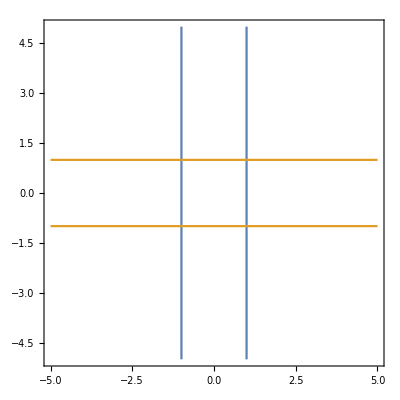

```mathematica
f1 =(x0 ^2- 1)
f2 = (x1^2 - 1)
ContourPlot[{f1 == 0, f2 ==0} ,{x0,-5,5},{x1,-5,5}]
```

1-2 u0^2+u0^4-2 u1^2-2 u0^2 u1^2+u1^4

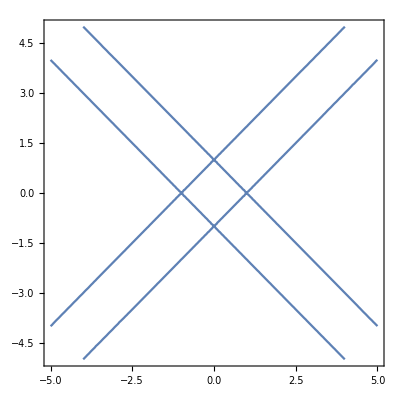

x1^2 - x2^2

```mathematica
h1 = ResourceFunction["PolynomialHomogenize"][Expand[f1],{x0, x1},x2];
h2 = ResourceFunction["PolynomialHomogenize"][Expand[f2],{x0, x1},x2];
h1 //InputForm
h2 //InputForm

d = u0^4-2*u0^2*u1^2+u1^4-2*u0^2*u2^2-2*u1^2*u2^2+u2^4;
s = d /. u2-> 1
ContourPlot[s == 0, {u0, -5, 5}, {u1, -5, 5}]
```